Visualizations of qubit driving beyond the RWA

## Original Hamiltonian & Magnus effective Hamiltonians

Define original Hamiltonian in the rotating frame

```mathematica
Horig:=H1/4*(Cos[phi]*sx+Cos[2*ww*t+phi]sx+Sin[phi]sy-Sin[2*ww*t+phi]*sy)+Delta/2*sz
```

Define Magnus approximation Hamiltonians

```mathematica
termHww0=1/4 (2 Delta sz+H1 sx Cos[phi]+H1 sy Sin[phi]);
termHwwM1=1/(32 ww)(H1^2 sz-2 H1^2 sz Cos[2 (phi+α0)]+4 (Delta H1 sx+H1D sy) Cos[phi+2 α0]+4 (H1D sx-Delta H1 sy) Sin[phi+2 α0]);
termHwwM2=1/(256 ww^2)(-8 Delta H1^2 sz-2 H1^3 sx Cos[phi]+8 Delta H1^2 sz Cos[2 (phi+α0)]-16 Delta^2 H1 sx Cos[phi+2 α0]+16 H1DD sx Cos[phi+2 α0]-32 Delta H1D sy Cos[phi+2 α0]+2 H1^3 sx Cos[3 phi+2 α0]-H1^3 sx Cos[3 phi+4 α0]-2 H1^3 sy Sin[phi]+24 H1 H1D sz Sin[2 (phi+α0)]-32 Delta H1D sx Sin[phi+2 α0]+16 Delta^2 H1 sy Sin[phi+2 α0]-16 H1DD sy Sin[phi+2 α0]+2 H1^3 sy Sin[3 phi+2 α0]+H1^3 sy Sin[3 phi+4 α0]);

Hww0=termHww0;
HwwM1=termHww0+termHwwM1;
HwwM2=termHww0+termHwwM1+termHwwM2;

ApproxHList={Hww0,HwwM1,HwwM2};
```

## Jump operators

```mathematica
jumpOww0=0;
jumpOwwM1=1/(4ww)ⅈ (HA-HB) Sin[α0-αj] (sx Cos[phi+α0+αj]-sy Sin[phi+α0+αj]);
jumpOwwM2=-1/(32 ww^2) ⅈ Sin[α0-αj] ((HA-HB) (HA+HB) sz Cos[α0-αj]
+2 (2 (Delta (HA-HB) sx+(HAD-HBD) sy) Cos[phi+α0+αj]+(-HA^2+HB^2) sz Cos[2 phi+α0+αj]+2 ((HAD-HBD) sx+Delta (-HA+HB) sy) Sin[phi+α0+αj]));

jumpOList=Accumulate[{jumpOww0,jumpOwwM1,jumpOwwM2}];
```

## Definition of the driving envelopes

```mathematica
(* Function definition format: list containing pairs of (end time of section, value of section), time starts at 0 *)
(* Time the drive is on lies between (0, 1), average value should be 1 *)
(* First element should always be {0, Function[t,0]} to get the initial jump right *)

drive1={
{0,Function[t,0]},
{1/2,Function[t,1/2]},
{1,Function[t,(3/2)-2(t-3/4)]}
};
drive2={
{0,Function[t,0]},
{1,Function[t,1]}
};
drive3={
{0,Function[t,0]},
{1/2,Function[t,4t]},
{1,Function[t,-4(t-1/2)+2]}
};
drive4={
{0,Function[t,0]},
{tr,Function[t,t/(tr-tr^2)]},
{1-tr,Function[t,1/(1-tr)]},
{1,Function[t,(1-t)/(tr-tr^2)]}
}/.{tr->0.2};
```

```mathematica
driveList={drive1,drive2,drive3,drive4};
```

```mathematica
driveListToPCFunction[dlist_]:=Function[t,Evaluate[Piecewise[{#[[2]][t],t<#[[1]]}&/@dlist,0]]];
```

```mathematica
PopupMenu[Dynamic[selDrive],Range[Length[driveList]]]
Dynamic[Plot[0.5*driveListToPCFunction[driveList[[selDrive]]][t/12.57],{t,-0.1*12.57,1.1*12.57},(*AxesLabel->{"t","H1"},*)PlotStyle->{Thick,Red},AxesStyle->Black,Method->{"AxesInFront" -> False}]]
```

## Drive envelope helper functions

## Trajectory integration and coordinate transformations

```mathematica
pms = {si->PauliMatrix[0],sx->PauliMatrix[1],sy->PauliMatrix[2],sz->PauliMatrix[3]};
ones2=ConstantArray[1,{2,2}];
H1Dsubs={
H1->(H1[t]),
H1D->(D[H1[t],{t,1}]),
H1DD->(D[H1[t],{t,2}]),
H1DDD->(D[H1[t],{t,3}]),
H1DDDD->(D[H1[t],{t,4}])
};

HAsubs={
HA->(HA[t]),
HAD->(D[HA[t],{t,1}]),
HADD->(D[HA[t],{t,2}]),
HADDD->(D[HA[t],{t,3}]),
HADDDD->(D[HA[t],{t,4}])
};

HBsubs={
HB->(HB[t]),
HBD->(D[HB[t],{t,1}]),
HBDD->(D[HB[t],{t,2}]),
HBDDD->(D[HB[t],{t,3}]),
HBDDDD->(D[HB[t],{t,4}])
};

AssembleH[H_,H1f_,vals_]:=(H/.vals/.H1Dsubs/.pms/.{H1->H1f});
ToHFunc[H_]:=Function[{t,α0},func]/.func->H;
GetHFunc[H_,H1f_,vals_]:=ToHFunc@AssembleH[H,H1f,vals];
```

```mathematica
(* Numerically compute trajectory from any Hamiltonian *)
NTrajectory[Hfunc_,tM_,α0_,ψ0_]:=
Module[{},
First@NDSolve[{(I*D[ψ[t],t]==Hfunc[t,α0].ψ[t])/.{Indeterminate->0},ψ[0]==ψ0},ψ,{t,0,tM}]
]

(* Helper functions for plotting *)
(* Coordinate transforms *)
BlochCoordinatesFromState=Function[{state},
{
Re[state[[1]]*state[[2]]*+state[[1]]*state[[2]]],
-Im[state[[1]]*state[[2]]*]+Im[state[[1]]**state[[2]]],
state[[1]]state[[1]]*-state[[2]]state[[2]]*
}];

RotationAxisFromHamiltonian=Function[{H},
Table[Re[Tr[H.PauliMatrix[i]]/2.],{i,1,3}]
];

(* Cartesian Bloch angles transformations *)
RestrictedAngleLeftPoint=-Pi/2;
RestrictAngle=Function[x,Mod[x-RestrictedAngleLeftPoint,2Pi]+RestrictedAngleLeftPoint];

BlochAngleCoordinatesFromState=Function[{state},
{
RestrictAngle[Arg[state[[2]]]-Arg[state[[1]]]],
2*ArcCos[Abs[state[[1]]]]-(Pi/2)
}
];

XBasisFromZBasis=Function[{state},
{
(state[[1]]+state[[2]])/Sqrt[2],
(state[[1]]-state[[2]])/Sqrt[2]
}
];

(* Mercator transformations *)
MercatorCoordinatesFromBlochAngle=Function[{coords},
{
coords[[1]],
-ArcTanh[Cos[coords[[2]]]]
}
];
```

## Arbitrary piecewise constant envelope functions

Numerically integrate wavefunction trajectories using a specified piecewise continuous (PC) drive envelope and a specified Hamiltonian (Ham). Between different continuous sections of the drive envelope, the specified jump operator is applied.
Returns many things:
[[1]]: piecewise continuous wavevector function ψ(t)
[[2]]: list of wavevector functions ψ_i(t) for each PC section of the drive envelope. Also valid outside the interval of the drive envelope PC section, there the drive envelope is extrapolated
[[3]]: list of wavevectors just before each jump
[[4]]: list of jump operator functions O(t) between subsequent drive envelope PC sections (i.e. the jump operators with the appropriate left-side and right-side drive functions plugged in)
[[5]]: piecewise continuous Hamiltonian with the appropriate drive envelopes plugged in
[[6]]: list of jump operator functions O(t) between drive envelope PC sections and the real trajectory

```mathematica
NPCTrajectory[pclist_,tM_,H1avg_,ψ0_,α0In_,Ham_,jumpOp_,vals_]:=Module[{
drive,evolOps,jumpOps,jumpTimes,jumpFuncs,Hfuncs,
nextHfunc,nextψafter,nextJumpTime,ψbefores,trajectories,nextTraj,trajectoryFunc,pcHFunc,finalJumpOps,finalJumpOpFunc
},
jumpTimes=pclist[[;;,1]]*tM; (* rescale all section times *)
jumpFuncs=Function[t,#[t/tM]*H1avg]&/@pclist[[;;,2]]; (* rescale each section function *)
jumpOps=Table[Function[tIn,Evaluate[((jumpOp/.pms)*ones2)/.HAsubs/.HBsubs/.{HA->jumpFuncs[[ii]],HB->jumpFuncs[[ii+1]],α0->α0In,αj->ww t}/.vals/.t->tIn]],{ii,Length[jumpTimes]-1}];

ψbefores={ψ0};
trajectories={Function[t,ψ0]};

Hfuncs=GetHFunc[Ham,#,vals]&/@jumpFuncs;

Do[
nextJumpTime=jumpTimes[[ii]];
nextψafter=MatrixExp[jumpOps[[ii]][jumpTimes[[ii]]]].Last[ψbefores];
(* the following could be optimized by restricting the time *)
nextTraj=ψ/.First@NDSolve[{(I*D[ψ[t],t]==Hfuncs[[ii+1]][t,α0In].ψ[t]),ψ[nextJumpTime]==nextψafter},ψ,{t,0,tM}]; 
trajectories=Insert[trajectories,nextTraj,-1];
ψbefores=Insert[ψbefores,nextTraj[jumpTimes[[ii+1]]],-1];
,
{ii,Length[jumpTimes]-1}
];

trajectoryFunc=Function[t,Evaluate[Piecewise[{#[[2]][t],t≤#[[1]]}&/@Transpose[{jumpTimes,trajectories}]]]];
pcHFunc=Function[t,Evaluate[Piecewise[{#[[2]][t,α0In],t≤#[[1]]}&/@Transpose[{Rest[jumpTimes],Rest[Hfuncs]}]]]];

(* calculate 'final' jump operators, that jump from each of the effective trajectories back to the real one *)
(* we make it jump back to the real one by putting HB to zero, such that the effective and real trajectories coincide on the right side of the jump *)
(* i.e. they both contain only the Delta sigma_z term and zeroth-order ME is exact *)
finalJumpOps=Table[Function[tIn,Evaluate[((jumpOp/.pms)*ones2)/.HAsubs/.HBsubs/.{HA->jumpFuncs[[ii]],HB->Function[t,0],α0->α0In,αj->ww t}/.vals/.t->tIn]],{ii,Length[jumpTimes]}];
finalJumpOpFunc=Function[t,Evaluate[Piecewise[{#[[2]][t],t≤#[[1]]}&/@Transpose[{jumpTimes,finalJumpOps}]]]];

Return[{trajectoryFunc,trajectories,ψbefores,jumpOps,pcHFunc,finalJumpOpFunc}];
]
```

```mathematica
(*test=NPCTrajectory[drive1,2Pi*1/0.9,0.9,{1.,0.},1.6,ApproxHList[[3]],jumpOList[[3]],{ww->1.0,Delta->0.0,phi->0.0}];

ParametricPlot3D[BlochCoordinatesFromState[test[[1]][t]],{t,-1,2Pi*1/0.9},PlotRange->{{-1,1},{-1,1},{-1,1}},Exclusions->{0,1/2*2Pi*1/0.9},ExclusionsStyle->Dashed]*)
```

## Plotting helper functions

```mathematica
(* Precompute the static bloch sphere elements (circumferences and axes) *)
BlochSphereCircles=With[{r=1},
{ParametricPlot3D[0.99*{r Cos[θ],r Sin[θ],0},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False],
ParametricPlot3D[0.99*{0,r Cos[θ],r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False],
ParametricPlot3D[0.99*{r Cos[θ],0,r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False]}
];
BlochSphereAxes=With[{r=1},{
Graphics3D[{
Thin, Gray, Dashed,
Line[{{-1.,0.,0.},{1.,0.,0.}}],
Line[{{0.,-1.,0.},{0.,1.,0.}}],
Line[{{0.,0.,-1.},{0.,0.,1.}}]
}]
}];

(* Plot trace on Bloch sphere *)
PlotBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot3D}]]:=
ParametricPlot3D[
BlochCoordinatesFromState[ψ[t]],
Evaluate[Join[{t},range]],
opts,PlotRange->{{-1,1},{-1,1},{-1,1}}
];

(* Plot a vector from the center of the Bloch sphere to the surface for a given state ψ *)
PlotBlochVectorFromState[ψ_,style_List :{}]:=PlotBlochVector[BlochCoordinatesFromState[ψ],style];

(* Plot a vector from the center of the Bloch sphere to the {x, y, z} coordinates given by vec *)
PlotBlochVector[vec_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Line[{{0.,0.,0.},vec}]}
]]];

(* Plot points given by a list of {x, y, z} tuples in pts *)
PlotBlochPoints[pts_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Point[pts]}
]]];

(* Plot points given by a list of state vectors ψs *)
PlotBlochPointsFromStates[ψs_,style_List : {}]:=PlotBlochPoints[Map[BlochCoordinatesFromState,ψs],style]

(* Plot BlochAngle trace *)
PlotBlochAngleTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot}]]:=
ParametricPlot[
BlochAngleCoordinatesFromState[ψ[t]],
Evaluate[Join[{t},range]],
opts
]/.Line[x_]:>Line@Split[x,Norm[#-#2]<1.5&](* This stuff is necessary to remove discontinuous jumps *);

(* Plot mercator Bloch trace *)
PlotMercatorBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot}]]:=
ParametricPlot[
MercatorCoordinatesFromBlochAngle[BlochAngleCoordinatesFromState[ψ[t]]],
Evaluate[Join[{t},range]],
opts
]/.Line[x_]:>Line@Split[x,Norm[#-#2]<1.5&](* This stuff is necessary to remove discontinuous jumps *);
```

## Plotting code

## 3D plots

```mathematica
Bloch3DPlotter:=Hold[
Show[
Join[
{ (* Plot the trajectory, state vector and instantaneous rotation axis of the qubit under the original Hamiltonian *)
PlotBlochTraceFromState[origTrace,{0,tM*tMax},PlotStyle->Red],
PlotBlochVectorFromState[origTrace[tM*tMax],{Red, Thickness[0.015]}],
PlotBlochVector[RotationAxisFromHamiltonian[hOrigFunc[tM*tMax,0.0]],{Gray,Thickness[0.010]}],
PlotBlochPointsFromStates[Map[origTrace,relevantTCoincidence],{PointSize[Large],Red}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochTraceFromState[approxTraces[[i]],{-1,tM*tMax},PlotStyle->approxColors[[ calculatedOrders[[i]] ]],Exclusions->jumpTimes,ExclusionsStyle->Dashed],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[PlotBlochPointsFromStates[Map[approxTraces[[i]],relevantTCoincidence],{PointSize[Large],approxColors[[ calculatedOrders[[i]] ]]}],{i,numSelectedOrders}],
(* Plot the t = t_f jump displacement *)
Table[PlotBlochTraceFromState[finalJumps[[ i ]], {0,1},PlotStyle->{Thin,Dashed, Black}],{i, numSelectedOrders}],
Table[PlotBlochPointsFromStates[{finalJumps[[ i ]][1]},{AbsolutePointSize[10],approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],
(*Table[PlotBlochTraceFromState[approxψ0[[i]], {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],*)
(*Table[PlotBlochTraceFromState[Function[t,finalJumps[[i]][t].approxTraces[[i]][tM*tMax]], {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],*)
(* Add static Bloch sphere elements *)
BlochSphereCircles,
BlochSphereAxes
],
ImageSize->{500,500},
ViewAngle->Pi/10,
Axes->False,
Boxed->False
]
];
```

## Cartesian Bloch angle plots

```mathematica
BlochAnglePlotter:=Hold[
Show[
Join[
{ (* Plot the trajectory and stroboscopic coincidence points of the qubit under the original Hamiltonian *)
PlotBlochAngleTraceFromState[XBasisFromZBasis@*origTrace,{0,tM*tMax},{PlotStyle->Red}],
Graphics[{PointSize[Large],Red,Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*origTrace)/@relevantTCoincidence]}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*(approxTraces[[i]]),{-1,tM*tMax},PlotStyle->approxColors[[ calculatedOrders[[i]] ]],Exclusions->jumpTimes,ExclusionsStyle->Dashed],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{PointSize[Large],approxColors[[ calculatedOrders[[i]] ]],Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*(approxTraces[[i]]))/@relevantTCoincidence]}],{i,numSelectedOrders}],

(* Plot the t = t_f jump displacement *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*finalJumps[[ i ]], {0,1},PlotStyle->{AbsoluteThickness[1.0],Dashed, Black}],{i, numSelectedOrders}],
Table[Graphics[{AbsolutePointSize[10],approxColors[[ calculatedOrders[[i]] ]],Point[BlochAngleCoordinatesFromState@XBasisFromZBasis@finalJumps[[i]][1]]}],{i,numSelectedOrders}]
],
PlotRange->{{-Pi,Pi},{0,Pi}},
AxesOrigin->{0,0},
AspectRatio->0.5,
ImageSize->{800,400},
AxesLabel->{"x-basis phase angle ϕ\nϕ = arg(<ψ|->) - arg(<ψ|+>)\n'longitude'","x-basis population angle θ\ncos(θ/2) = |<ψ|+>|\n'latitude'"},
PlotLabel->"Bloch angle coordinates in the X-basis"
]
];
```

## Mercator plots

```mathematica
BlochMercatorPlotter:=Hold[
Show[
Join[
{ (* Plot the trajectory and stroboscopic coincidence points of the qubit under the original Hamiltonian *)
PlotMercatorBlochTraceFromState[XBasisFromZBasis@*origTrace,{0,tM*tMax},PlotStyle->Red],
Graphics[{PointSize[Large],Red,Point[MercatorCoordinatesFromBlochAngle/@BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*origTrace)/@relevantTCoincidence]}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotMercatorBlochTraceFromState[XBasisFromZBasis@*(approxTraces[[i]]),{-1,tM*tMax},PlotStyle->approxColors[[ calculatedOrders[[i]] ]],Exclusions->jumpTimes,ExclusionsStyle->Dashed],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{PointSize[Large],approxColors[[ calculatedOrders[[i]] ]],Point[MercatorCoordinatesFromBlochAngle/@BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*(approxTraces[[i]]))/@relevantTCoincidence]}],{i,numSelectedOrders}],
(* Plot the t = t_f jump displacement *)
Table[PlotMercatorBlochTraceFromState[XBasisFromZBasis @*finalJumps[[ i ]], {0,1},PlotStyle->{AbsoluteThickness[1.0],Dashed, Black}],{i, numSelectedOrders}],
Table[Graphics[{AbsolutePointSize[10],approxColors[[ calculatedOrders[[i]] ]],Point[MercatorCoordinatesFromBlochAngle@BlochAngleCoordinatesFromState@XBasisFromZBasis@finalJumps[[i]][1]]}],{i,numSelectedOrders}]
],
AspectRatio->0.5,
ImageSize->{800,400},
PlotRange->{{-Pi,Pi},{-0.5,0.5}},
AxesLabel->{"Mercator longitude ϕ,\nx-basis phase angle ϕ\nϕ = arg(<ψ|->) - arg(<ψ|+>)\n","Mercator z-intersect z(θ),\nx-basis population angle θ\ncos(θ/2) = |<ψ|+>|"}
]
];
```

## Interactive trajectory manipulation code

```mathematica
approxColors=Array[ColorData["BlueGreenYellow"],Length[ApproxHList],{0.2,1.}];
(*approxColors=Table[RGBColor[1.0-ii,ii,ii],{ii,Subdivide[0.0,1.0,Length[ApproxHList]]}];*)

InteractiveTrajectoryPlotting[plotExprs_List]:=
DynamicModule[{origTrace,approxTraces,ψ0,gateAngle,tMax,H1func,vals,hOrigFunc,
tCoincidence,t0,tC,relevantTCoincidence,selectedDrive,selectedDriveFunc,selectedH1Index,numSelectedOrders,
selectedJmpOperators,approxψ0,jmpFuncs,calculatedOrders,finalJumps,approxTracesAll,origAll,jumpTimes,finalJumpOpFuncs},
Column[{
Row[{Text["Select driving envelope:  "],PopupMenu[Dynamic[selectedH1Index],Range[Length[driveList]]],
Dynamic[Plot[driveListToPCFunction[driveList[[selectedH1Index]]][t],{t,-0.1,1.1},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)",ImageSize->Medium]]}],
Manipulate[
(* Define initial state and desired gate angle *)
ψ0={1,0};
ψ0=ψ0/Norm[ψ0];
gateAngle = Pi;
tMax = 2*gateAngle/H1avg;
Dynamic[selectedH1Index];
selectedDrive=driveList[[selectedH1Index]];
selectedDriveFunc=driveListToPCFunction[selectedDrive];
H1func=Function[t,selectedDrive[t/tMax]*H1avg];
vals ={ww->wwIn,Delta->DeltaIn,phi->phiIn};

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
t0=(α0/ww)/.vals;
tC=(Pi/ww)/.vals;
tCoincidence=t0+Range[0.0,tMax,tC];

(* This is a little trick to keep the changing of parameters smooth *)
(* Without it, the inner dynamic block would get updated upon change of selectedOrders, *)
(* before the outer block. Specifically, the inner dynamic block would try to plot the new orders, *)
(* before their trajectories were calculated in the outer block. *)
calculatedOrders=selectedOrders;
numSelectedOrders=Length[calculatedOrders];

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
origAll=NPCTrajectory[selectedDrive,tMax,H1avg,ψ0,α0,Horig,0,vals];
hOrigFunc=origAll[[5]];
origTrace=origAll[[1]];

approxTracesAll=Table[NPCTrajectory[selectedDrive,tMax,H1avg,ψ0,α0,ApproxHList[[ calculatedOrders[[i]] ]],jumpOList[[ calculatedOrders[[i]] ]],vals],{i,numSelectedOrders}];
approxTraces=approxTracesAll[[;;,1]];
jumpTimes=selectedDrive[[;;,1]]*tMax;
finalJumpOpFuncs=approxTracesAll[[;;,6]];

(* Let's get plottin'! *)
Dynamic[
relevantTCoincidence=Select[tCoincidence,(#<tM*tMax&)];

finalJumps=Table[Function[jmpFraction,
Evaluate[MatrixExp[jmpFraction*(finalJumpOpFuncs[[ ii ]])[tM*tMax]] . (approxTraces[[ ii ]])[tM*tMax]]
],{ii,numSelectedOrders}];
Grid[{Table[ReleaseHold[plotExprs[[i,1]]],{i,selectedPlots}],
{StringForm["t_gate = ``", NumberForm[tMax,{5,2}]]}}
]
]
,
{{tM, 0.01,"Time t / t_gate"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{α0,0.0,"Offset α0"},0.0, Pi,Appearance->"Open"},
{{H1avg, 0.2,"Average drive strength H1_avg"},0.01,2.0,Appearance->"Open"},
(*{{upToOrder,1,"Include Magnus expansion up to order"},-1,Length[ApproxHList]-1,1,Appearance->"Open"},*)
{
{selectedOrders,{1,2},"Show Magnus orders"},
(#->Graphics[{Text[#-1],EdgeForm[Thin],approxColors[[#]],Rectangle[{1,-0.5}]},ImageSize->{30,12}])&/@Range[1,Length[ApproxHList]],
ControlType->CheckboxBar
},
{{wwIn,1.0,"Drive frequency ω"},0.01,2.0},
{{DeltaIn,0.0,"Qubit detuning Δ"},-1.0,1.0},
{{phiIn,0.0,"Rotation axis angle ϕ"},-Pi,Pi},
{{selectedPlots,Pick[Range[Length[plotExprs]],plotExprs[[;;,3]],1],"Visualizations"},Table[i->plotExprs[[i,2]],{i,Length[plotExprs]}],ControlType->CheckboxBar}
(*Evaluate[Sequence@@Table[{{selplots[i],plotExprs[[i,3]],plotExprs[[i,2]]},{0,1}},{i,Length[plotExprs]}]]*)
]}]
]
```

## The final plot!

```mathematica
InteractiveTrajectoryPlotting[{
{Bloch3DPlotter,"3D",1}, 
{BlochAnglePlotter,"Cartesian Bloch angle",0}
(*{BlochMercatorPlotter,"Mercator",0}*)
}]
```

## Customized plots

```mathematica
DynamicModule[{origTrace,approxTraces,ψ0,gateAngle,tMax,H1func,vals,hOrigFunc,
tCoincidence,t0,tC,relevantTCoincidence,selectedDrive,selectedDriveFunc,selectedH1Index,numSelectedOrders,
selectedJmpOperators,approxψ0,jmpFuncs,calculatedOrders,finalJumps,approxTracesAll,origAll,jumpTimes,finalJumpOpFuncs},
Column[{
Row[{Text["Select driving envelope:  "],PopupMenu[Dynamic[selectedH1Index],Range[Length[driveList]]],
Dynamic[Plot[driveListToPCFunction[driveList[[selectedH1Index]]][t],{t,-0.1,1.1},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)",ImageSize->Medium]]}],
Manipulate[
(* Define initial state and desired gate angle *)
ψ0={1,0};
ψ0=ψ0/Norm[ψ0];
gateAngle = Pi;
tMax = 2*gateAngle/H1avg;
Dynamic[selectedH1Index];
selectedDrive=driveList[[selectedH1Index]];
selectedDriveFunc=driveListToPCFunction[selectedDrive];
H1func=Function[t,selectedDrive[t/tMax]*H1avg];
vals ={ww->wwIn,Delta->DeltaIn,phi->phiIn};

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
t0=(α0/ww)/.vals;
tC=(Pi/ww)/.vals;
tCoincidence=t0+Range[0.0,tMax,tC];

(* This is a little trick to keep the changing of parameters smooth *)
(* Without it, the inner dynamic block would get updated upon change of selectedOrders, *)
(* before the outer block. Specifically, the inner dynamic block would try to plot the new orders, *)
(* before their trajectories were calculated in the outer block. *)
calculatedOrders=selectedOrders;
numSelectedOrders=Length[calculatedOrders];

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
origAll=NPCTrajectory[selectedDrive,tMax,H1avg,ψ0,α0,Horig,0,vals];
hOrigFunc=origAll[[5]];
origTrace=origAll[[1]];

approxTracesAll=Table[NPCTrajectory[selectedDrive,tMax,H1avg,ψ0,α0,ApproxHList[[ calculatedOrders[[i]] ]],jumpOList[[ calculatedOrders[[i]] ]],vals],{i,numSelectedOrders}];
approxTraces=approxTracesAll[[;;,1]];
jumpTimes=selectedDrive[[;;,1]]*tMax;
finalJumpOpFuncs=approxTracesAll[[;;,6]];

(* Let's get plottin'! *)
Dynamic[
relevantTCoincidence=Select[tCoincidence,(#<tM*tMax&)];

finalJumps=Table[Function[jmpFraction,
Evaluate[MatrixExp[jmpFraction*(finalJumpOpFuncs[[ ii ]])[tM*tMax]] . (approxTraces[[ ii ]])[tM*tMax]]
],{ii,numSelectedOrders}];
Grid[{
{Show[
Join[
{ (* Plot the trajectory and stroboscopic coincidence points of the qubit under the original Hamiltonian *)
PlotBlochAngleTraceFromState[XBasisFromZBasis@*origTrace,{0,tM*tMax},{PlotStyle->Red}],
Graphics[{AbsolutePointSize[12],Red,Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*origTrace)/@relevantTCoincidence]}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*(approxTraces[[i]]),{-1,tM*tMax},PlotStyle->Blue,Exclusions->jumpTimes,ExclusionsStyle->Dashed],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{PointSize[Large],Blue,Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*(approxTraces[[i]]))/@relevantTCoincidence]}],{i,numSelectedOrders}],
{
ListPlot[{BlochAngleCoordinatesFromState@XBasisFromZBasis@origTrace[jumpTimes[[2]]]},(*PlotMarkers->Style["◆",FontSize->15],*)PlotStyle->Red],
ListPlot[{BlochAngleCoordinatesFromState@XBasisFromZBasis@approxTracesAll[[1,2,2]][jumpTimes[[2]]]},(*PlotMarkers->Style["◆",FontSize->15],*)PlotStyle->Blue],
ListPlot[{BlochAngleCoordinatesFromState@XBasisFromZBasis@approxTracesAll[[1,2,3]][jumpTimes[[2]]]},(*PlotMarkers->Style["◆",FontSize->15],*)PlotStyle->Blue]
},

(* Plot the t = t_f jump displacement *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*finalJumps[[ i ]], {0,1},PlotStyle->{AbsoluteThickness[1.0],Dashed, Black}],{i, numSelectedOrders}],
Table[Graphics[{AbsolutePointSize[10],approxColors[[ calculatedOrders[[i]] ]],Point[BlochAngleCoordinatesFromState@XBasisFromZBasis@finalJumps[[i]][1]]}],{i,numSelectedOrders}]
],
PlotRange->{{0,3.3},{-0.1,0.2}},
AxesOrigin->{0,0},
LabelStyle->Black,
AxesStyle->Black,
TicksStyle->Black,
AspectRatio->0.2
(*ImageSize->{800,400},*)
(*FrameLabel->{"Rotated Bloch sphere longitude ϕ\nϕ = arg(<ψ|->) - arg(<ψ|+>)","Rotated Bloch sphere latitude θ\ncos((θ + π/2) / 2) = |<ψ|+>|"}*)
(*Framed->True*)
]}
,
{StringForm["t_gate = ``", NumberForm[tMax,{5,2}]]},
{Transpose@{BlochAngleCoordinatesFromState@XBasisFromZBasis@origTrace[jumpTimes[[2]]]}}
}
]
]
,
{{tM,1.0,"Time t / t_gate"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{α0,0.9,"Offset α0"},0.0, Pi,Appearance->"Open"},
{{H1avg, 0.5,"Average drive strength H1_avg"},0.01,2.0,Appearance->"Open"},
(*{{upToOrder,1,"Include Magnus expansion up to order"},-1,Length[ApproxHList]-1,1,Appearance->"Open"},*)
{
{selectedOrders,{3},"Show Magnus orders"},
(#->Graphics[{Text[#-1],EdgeForm[Thin],approxColors[[#]],Rectangle[{1,-0.5}]},ImageSize->{30,12}])&/@Range[1,Length[ApproxHList]],
ControlType->CheckboxBar
},
{{wwIn,1.0,"Drive frequency ω"},0.01,2.0},
{{DeltaIn,0.0,"Qubit detuning Δ"},-1.0,1.0},
{{phiIn,0.0,"Rotation axis angle ϕ"},-Pi,Pi}
(*Evaluate[Sequence@@Table[{{selplots[i],plotExprs[[i,3]],plotExprs[[i,2]]},{0,1}},{i,Length[plotExprs]}]]*)
]}]
]
```

```mathematica
Cos[(th-Pi)/2]//FullSimplify
```

Sin[th/2]

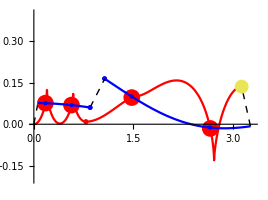
```mathematica
-Graphics-/.(AxesStyle->Black)->Sequence[AxesStyle->Black,TicksStyle->Black]
```

-Graphics-

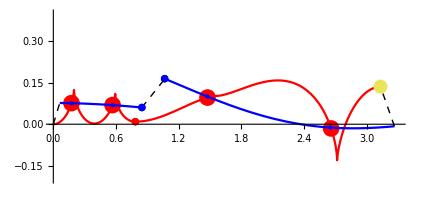
```mathematica
-Graphics-/.(PlotRange->we_):>(PlotRange->{-0.1,0.2})/.(AspectRatio->we_):>(AspectRatio->1)
```

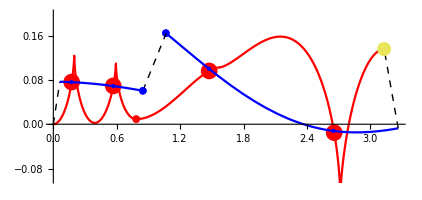

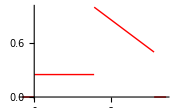
```mathematica
-Graphics-/.(AxesStyle->Black)->Sequence[AxesStyle->Black,TicksStyle->Black]
```

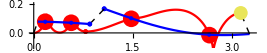
```mathematica
-Graphics--Graphics-
```